# Monte Carlo Integration

## 1. Case of a 1D positive function

### 1.1 Function definition

Define the interval I want to integrate my function over

```mathematica
{xMin,xMax}={-1,4}
```

{-1,4}

Pick any function you want here, as long as it only takes positive values over the range

```mathematica
f[x_]=12-2x-3 x^2+x^3
```

12-2 x-3 x^2+x^3

I plot my function here

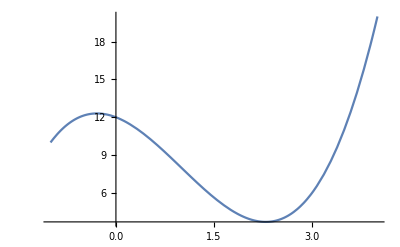

```mathematica
Plot[f[x],{x,xMin,xMax}]
```

Here, me know that the function is positive, so I can take yMin=0.  The true max value of Y is reached at xMax (true value is y=20).  Here I am being conservative on purpose, just to show you that I don’t need to work with the exact values, and pick yMin=0, yMax=25  The price I will pay for excess of caution is loss of precision for the same number of random data points (more on that later).

```mathematica
{yMin,yMax}={0,25}
```

{0,25}

Verify that my plot all fits in

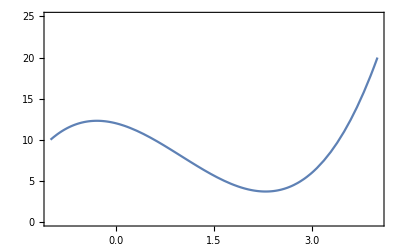

```mathematica
funcPlot=Plot[f[x],{x,xMin,xMax},PlotRange->{{xMin,xMax},{yMin,yMax}},Frame->True]
```

### 1.2 Compute exact integral

```mathematica
g[x_]=Integrate[f[x],x]
```

12 x-x^2-x^3+x^4/4

```mathematica
N[g[xMax]-g[xMin]]
```

43.75

```mathematica
trueIntegral=Integrate[f[x],{x,xMin,xMax}]//N
```

43.75

### 1.3 Monte Carlo integration

#### 1.3.1 Generation of data points in the range [xMin, xMax]x[yMin, yMax]

```mathematica
ptInRange[minX_,maxX_,minY_,maxY_]:={RandomReal[{minX,maxX}], RandomReal[{minY,maxY}]}
```

#### 1.3.2 Now compute the integral

```mathematica
MonteCarloIntegrate[xMin_,xMax_,yMin_,yMax_,maxCount_,printSteps_]:=
Block[
{x,y,
k,
belowCount=0
},
For[k=1,k≤maxCount,k++,
{x,y}=ptInRange[xMin,xMax,yMin,yMax];
If [f[x] ≥y,
belowCount++];
If [Mod[k,printSteps]==0,
Print["k=",k," → ",belowCount,"/",k," = ",N[belowCount/k],", ∫ = ",N[(xMax-xMin)*(yMax-yMin)*belowCount/k]]
];
];
 N[(xMax-xMin)*(yMax-yMin)*belowCount/maxCount]
]
```

```mathematica
MonteCarloIntegrate[xMin,xMax,yMin,yMax,10000,500]
```

k=500 → 189/500 = 0.378, ∫ = 47.25

k=1000 → 362/1000 = 0.362, ∫ = 45.25

k=1500 → 545/1500 = 0.363333, ∫ = 45.4167

k=2000 → 712/2000 = 0.356, ∫ = 44.5

k=2500 → 870/2500 = 0.348, ∫ = 43.5

k=3000 → 1046/3000 = 0.348667, ∫ = 43.5833

k=3500 → 1212/3500 = 0.346286, ∫ = 43.2857

k=4000 → 1386/4000 = 0.3465, ∫ = 43.3125

k=4500 → 1568/4500 = 0.348444, ∫ = 43.5556

k=5000 → 1749/5000 = 0.3498, ∫ = 43.725

k=5500 → 1919/5500 = 0.348909, ∫ = 43.6136

k=6000 → 2097/6000 = 0.3495, ∫ = 43.6875

k=6500 → 2278/6500 = 0.350462, ∫ = 43.8077

k=7000 → 2475/7000 = 0.353571, ∫ = 44.1964

k=7500 → 2665/7500 = 0.355333, ∫ = 44.4167

k=8000 → 2853/8000 = 0.356625, ∫ = 44.5781

k=8500 → 3011/8500 = 0.354235, ∫ = 44.2794

k=9000 → 3181/9000 = 0.353444, ∫ = 44.1806

k=9500 → 3339/9500 = 0.351474, ∫ = 43.9342

k=10000 → 3502/10000 = 0.3502, ∫ = 43.775

43.775

#### 1.3.3 Pre-generate a bunch of data points in the range [xMin, xMax]x[yMin, yMax]

```mathematica
nbPts=10000;
dataPts=Table[ptInRange[xMin,xMax,yMin,yMax],{k,1,nbPts}];
```

#### 1.3.4 Interactive plot

```mathematica
Manipulate[
Block[
{
above={},
below={},
mPt,
intEval
},
(* split the partial data list into "above" and "below" point lists *)
For[k=1,k≤n,k++,
mPt=dataPts[[k]];
If[f[mPt[[1]]]≤mPt[[2]],
below=Append[below,mPt],
above=Append[above,mPt]
];
intEval=N[Dimensions[below][[1]]*(xMax-xMin)*(yMax-yMin)/n];
];
ListPlot[{below,above},PlotRange->{{xMin,xMax},{yMin,yMax}},PlotStyle->PointSize[0.01],PlotLegends->{Dimensions[below][[1]]/n,intEval}]
],
{n,nbPts/100,nbPts}]
```